```mathematica
(*Name: Md. Asraful Islam*)
(*Roll No :AE-123-051*)
```

```mathematica
(*Question No 1a*)
```

```mathematica
setA=Range[3]
```

{1,2,3}

```mathematica
(*Question No 1b*)
```

```mathematica
setB=Select[Range[12],OddQ]
```

{1,3,5,7,9,11}

```mathematica
(*Question No 1c*)
```

```mathematica
setC=Select[Fibonacci[Range[20]],#<1000&&PrimeQ[#]&]
```

{2,3,5,13,89,233}

```mathematica
(*Qusestion No 2a*)
```

```mathematica
MemberQ[{1,3,5,7},3]
```

True

```mathematica
(*Question No 2b*)
```

```mathematica
MemberQ[{2,4,6,8},6]
```

True

```mathematica
(*Question No 2c*)
```

```mathematica
MemberQ[Range[16],10]
```

True

```mathematica
(*Question No 2d*)
```

```mathematica
Not[MemberQ[Range[16],11]]
```

False

```mathematica
(*Question No 2e*)
```

```mathematica
Not[MemberQ[Select[Range[10],EvenQ],4]]
```

False

```mathematica
Exit[]
```

```mathematica
(*Question No 03*)
```

```mathematica
(*Define three circular regions*)
A=Disk[{0,0},2];
B=Disk[{2,0},2];
F=Disk[{1,2},2];
```

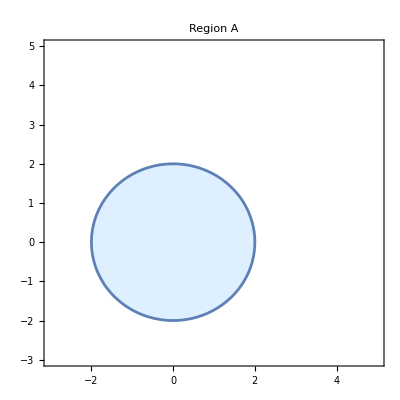

```mathematica
(*a) Region A*)
RegionPlot[RegionMember[A][{x,y}],{x,-3,5},{y,-3,5},PlotLabel->"Region A",PlotStyle->LightBlue]
```

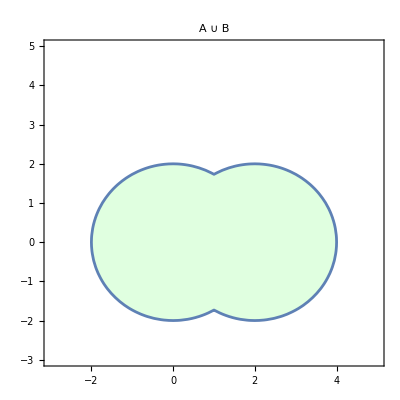

```mathematica
(*b) A ∪ B*)
RegionPlot[RegionMember[RegionUnion[A,B]][{x,y}],{x,-3,5},{y,-3,5},PlotLabel->"A ∪ B",PlotStyle->LightGreen]
```

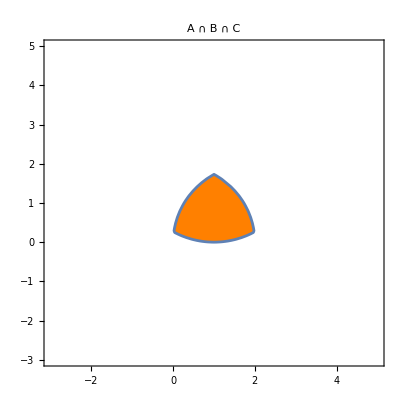

```mathematica
(*c) A ∩ B ∩ C*)
RegionPlot[RegionMember[RegionIntersection[A,B,F]][{x,y}],{x,-3,5},{y,-3,5},PlotLabel->"A ∩ B ∩ C",PlotStyle->Orange]
```

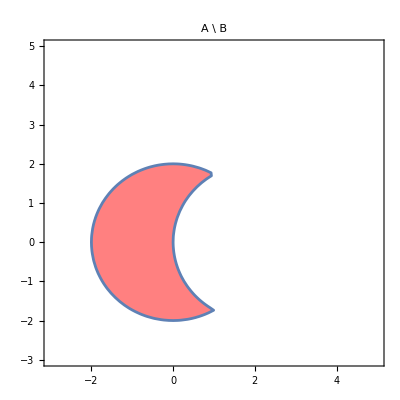

```mathematica
(*d) A\B*)
RegionPlot[RegionMember[RegionDifference[A,B]][{x,y}],{x,-3,5},{y,-3,5},PlotLabel->"A \\ B",PlotStyle->Pink]
```

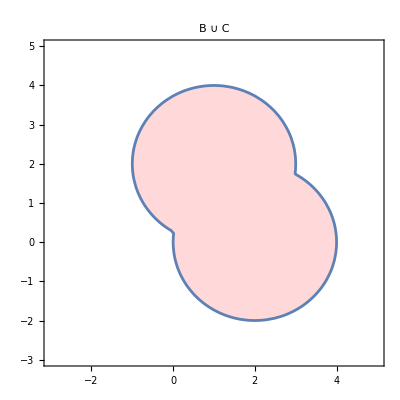

```mathematica
(*e) B ∪ C*)
RegionPlot[RegionMember[RegionUnion[B,F]][{x,y}],{x,-3,5},{y,-3,5},PlotLabel->"B ∪ C",PlotStyle->LightRed]
```

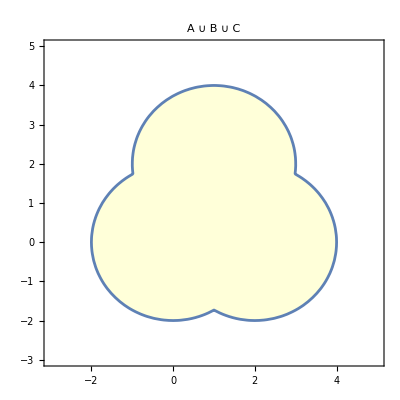

```mathematica
(*f) A ∪ B ∪ C*)
RegionPlot[RegionMember[RegionUnion[A,B,F]][{x,y}],{x,-3,5},{y,-3,5},PlotLabel->"A ∪ B ∪ C",PlotStyle->LightYellow]
```

```mathematica
(*Question No 04*)
```

```mathematica
setA={c};
setB={a,b};
setC={b,d};
setU={a,b,c,d,e,f};
```

```mathematica
(*A U (B' U C')*)
```

```mathematica
Union[setA,Intersection[Complement[setU,setB],Complement[setU,setC]]]
```

{c,e,f}

```mathematica
(*(A U B') ^ (A ^ C')*)
```

```mathematica
Intersection[Union[setA,Complement[setU,setB]],Union[setA,Complement[setU,setC]]]
```

{c,e,f}

```mathematica
Exit[]
```

```mathematica
(*Questoin No 05*)
```

```mathematica
setA={1,3,4,5,6};
setB={2,4,7,8};
setU={1,2,3,4,5,6,7,8,9,11};
```

```mathematica
LHS=Complement[setU,Union[setA,setB]]
RHS=Intersection[Complement[setU,setA],Complement[setU,setB]]
```

{9,11}

{9,11}

```mathematica
(*Question No 06*)
```

```mathematica
d=150;
m=140;
s=120;
dm=60;
ds=50;
ms=40;
dms=25;
total=300;
```

```mathematica
(*a*)
```

```mathematica
exactly1=(d-dm-ds+dms)+(m-dm-ms+dms)+(s-ds-ms+dms)
```

185

```mathematica
(*b*)
```

```mathematica
exactly2=(dm-dms)+(ds-dms)+(ms-dms)
```

75

```mathematica
(*c*)
```

```mathematica
atleast1=d+m+s-dm-ds-ms+dms
```

285

```mathematica
(*d*)
```

```mathematica
none=total-atleast1
```

15

```mathematica
(*Question No 07*)
```

```mathematica
c[m_]:=Piecewise[{{0.5m,m<=100},{50+0.3m,100<m<=300},{110+0.2m,m>300}}];
avg[m_]:=c[m]/m;
```

```mathematica
c[80]
avg[80]
```

40.

0.5

```mathematica
c[150]
avg[150]
```

95.

0.633333

```mathematica
c[450]
avg[450]
```

200.

0.444444

```mathematica
Exit[]
```

```mathematica
(*Question No 08*)
```

```mathematica
num={6944,7245,21408};
Table[{n,Divisible[n,2],Divisible[n,3],FactorInteger[n]},{n,num}]//TableForm[#,TableHeadings->{None, {"Number","Divisible by 2","Divisible by 3","Primefactorization"}},TableAlignments->Center]&
```

Number | Divisible by 2 | Divisible by 3 | Primefactorization
6944 | True | False | 2 | 5
7 | 1
31 | 1
7245 | False | True | 3 | 2
5 | 1
7 | 1
23 | 1
21408 | True | True | 2 | 5
3 | 1
223 | 1

```mathematica
Exit
```

```mathematica
(*Question No 09*)
```

```mathematica
number={41,43,107,113};
Table[{n,PrimeQ[n]&&PrimeQ[FromDigits[Reverse[IntegerDigits[n]]]]&&FromDigits[Reverse[IntegerDigits[n]]]!=n},{n,number}]//TableForm[#,TableHeadings->{None, {"Number","Emirp"}},TableAlignments->Center]&
```

Number | Emirp
41 | False
43 | False
107 | True
113 | True

```mathematica
(*Question No 10*)
```

```mathematica
a=Input[a];
b=Input[b];
g=GCD[a,b]
l=LCM[a,b]
product1=a*b
product2=g*l
conjecture=product1==product2
```

24

144

3456

3456

True

```mathematica
(*Question No 11*)
```

```mathematica
Clear[skyClear,sundown,seeSaturn]
```

```mathematica
exp1=Implies[skyClear&&sundown,seeSaturn];
exp2=Implies[!skyClear||!sundown,!seeSaturn];
Table[{skyClear,sundown,seeSaturn,exp1,exp2},{skyClear,{True,False}},{sundown,{True,False}},{seeSaturn,{True,False}}]//Flatten[#,2]&//TableForm[#,TableHeadings->{None, {"skyclear","sundown","seeSaturn","exp1","exp2"}}]&
```

skyclear | sundown | seeSaturn | exp1 | exp2
True | True | True | True | True
True | True | False | False | True
True | False | True | True | False
True | False | False | True | True
False | True | True | True | False
False | True | False | True | True
False | False | True | True | False
False | False | False | True | True

```mathematica
Exit
```

```mathematica
(*Question No 12*)
```

```mathematica
Clear[fedex,ups,ontime]
```

```mathematica
stat1=fedex->!ups&&ontime;
stat2=ontime<->fedex||!ups;
stat3=Implies[!fedex,!ups&&ontime];
Table[{fedex,ups,ontime,stat1,stat2,stat3},{fedex,{True,False}},{ups,{True,False}},{ontime,{True,False}}]//Flatten[#,2]&//TableForm[#,TableHeadings->{None, {"Fedex","UPS","ontime","statement 1","statement 2","statement 3"}},TableAlignments->Center]&
```

Fedex | UPS | ontime | statement 1 | statement 2 | statement 3
True | True | True | True→False | True<->True | True
True | True | False | True→False | False<->True | True
True | False | True | True→True | True<->True | True
True | False | False | True→False | False<->True | True
False | True | True | False→False | True<->False | False
False | True | False | False→False | False<->False | False
False | False | True | False→True | True<->True | True
False | False | False | False→False | False<->True | False

```mathematica
Exit
(*Question No 13*)
```

```mathematica
gradePoint[mark_]:=Which[mark>=80,4.0,mark>=75,3.75,mark>=70,3.5,mark>=65,3.25,mark>=60,3.0,mark>=55,2.75,mark>=50,2.5,mark>=45,2.25,mark>=40,2.0,True,0.0];

courses={"A101","A102","A103","A104","A105","A106","A107","A150"};
marks={76,82,68,78,87,67,58,80};
credits={3,4,3,4,3,3,3,3}; 

gpas=gradePoint/@marks;
weightedGPA=gpas*credits;

(*table*)
studentTable=Prepend[Transpose[{courses,marks,gpas,credits,weightedGPA}],{"Course","Marks","GPA","Credit Hours","GPA × Credit"}];

Grid[studentTable,Frame->All,Alignment->Center,Background->{None,{LightBlue,None}}]

(*Calculate CGPA*)
totalCredits=Total[credits];
totalWeightedGPA=Total[weightedGPA];
cgpa=totalWeightedGPA/totalCredits;
Print["The total CGPS is: ",cgpa]
```

Course | Marks | GPA | Credit Hours | GPA × Credit
A101 | 76 | 3.75 | 3 | 11.25
A102 | 82 | 4. | 4 | 16.
A103 | 68 | 3.25 | 3 | 9.75
A104 | 78 | 3.75 | 4 | 15.
A105 | 87 | 4. | 3 | 12.
A106 | 67 | 3.25 | 3 | 9.75
A107 | 58 | 2.75 | 3 | 8.25
A150 | 80 | 4. | 3 | 12.

The total CGPS is: 3.61538

```mathematica
Exit
```